# Ibraheem Al-Yousef PHYS430 HW.3

## Problem 1):

```mathematica
Mac[q_]:=Binomial[q+143-1,q]*Binomial[90-q+55-1,90-q];
max:=Reverse@{Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]]//Max,Position[Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]],Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]]//Max][[1]][[1]]-1};
min:=Reverse@{Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]]//Min,Position[Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]],Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]]//Min][[1]][[1]]-1};
```

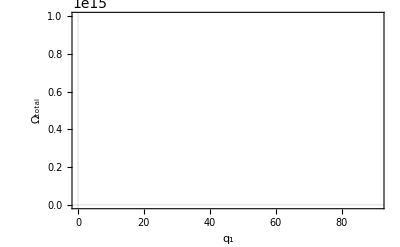

```mathematica
ListLinePlot[Table[Mac[q],{q,0,90,1}],PlotTheme->"Scientific",FrameLabel->{"q_1","Ω_total"},PlotStyle->Black]
```

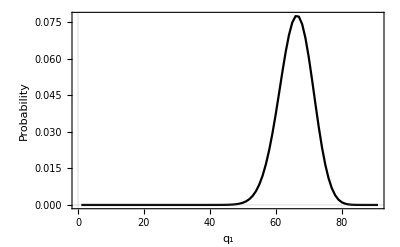

```mathematica
ListLinePlot[Table[Mac[q],{q,0,90,1}]/Total[Table[Mac[q],{q,0,90,1}]],PlotTheme->"Scientific",FrameLabel->{"q_1","Probability"},PlotStyle->Black]
```

```mathematica
max//N
min//N
```

{65.,0.0775195}

{0.,9.62927×10^-37}

The most probable macrostate is at q_1=65, with a probability of 0.08. The least probable macrostate is ay q_1=0 with a probability of 9.6×10^-37

## Problem 2):

### The plots:

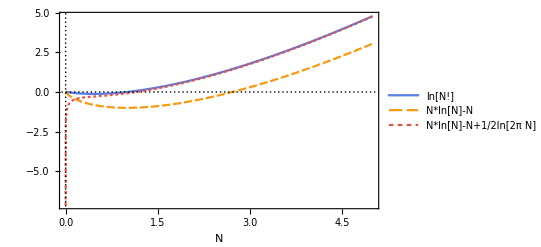

```mathematica
Plot[{Log[s!],s*Log[s]-s,s*Log[s]-s+1/2 Log[2π s]},{s,0,5},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"N",""},PlotLegends->{"ln[N!]","N*ln[N]-N","N*ln[N]-N+1/2ln[2π N]"}]
```

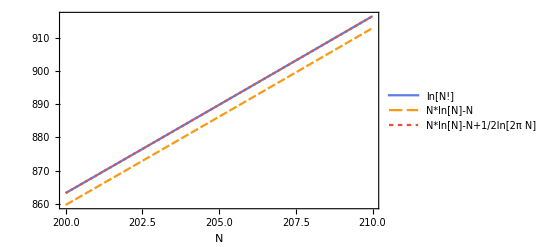

```mathematica
Plot[{Log[s!],s*Log[s]-s,s*Log[s]-s+1/2 Log[2π s]},{s,200,210},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"N",""},PlotLegends->{"ln[N!]","N*ln[N]-N","N*ln[N]-N+1/2ln[2π N]"}]
```

### Percentage difference, which is defined as (|v1-v2|)/[(v1+v2)/2]*100% :

```mathematica
SetAttributes[Pdiff,HoldAll];
Pdiff[f1_,f2_]:="The %Diff between "<>ToString[HoldForm[f1]//TraditionalForm]<>" and "<>ToString[HoldForm[f2]//TraditionalForm]<>" is: "<>ToString[Abs[f1-f2]/((f1+f2)/2)*100//N,TraditionalForm]<>"%"//TraditionalForm
```

```mathematica
n=1*10^4;
```

```mathematica
Pdiff[Log[n!],n*Log[n]-n]
Pdiff[Log[n!],n*Log[n]-n+1/2 Log[2π n]]
Pdiff[n!,n*Exp[-n]]//Quiet
Pdiff[n!,n*Exp[-n]*√(2π*n)]//Quiet
```

The %Diff between log(n!) and n log(n)-n is: 0.00672802%

The %Diff between log(n!) and n log(n)-n+1/2 log(2 π n) is: 1.01491×10^-8%

The %Diff between n! and n exp(-n) is: 200.%

The %Diff between n! and n exp(-n) √(2 π n) is: 200.%

## Problem 3):

```mathematica
apmac[q_,s_,qm_]:=(E/s)^(2s)*(q*(qm-q))^s;
ap2mac[q_,s_,qm_]:=(E/s)^(2s)*(qm/2)^(2s)*Exp[-s*((2z)/qm)^2]/.z->q-qm/2;
```

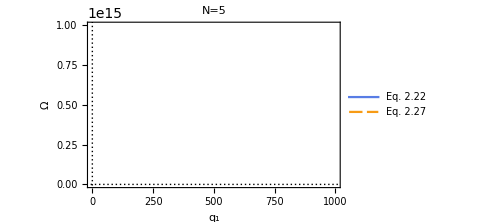

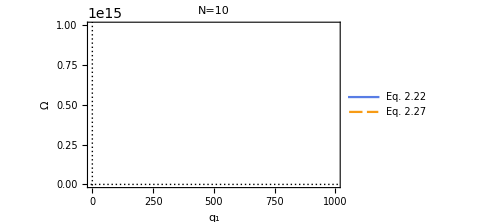

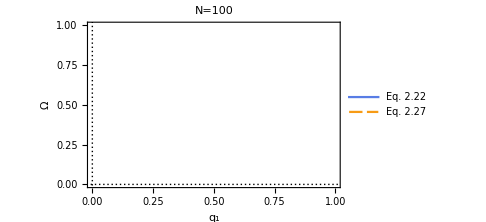

```mathematica
Plot[{apmac[q,5,1000],ap2mac[q,5,1000]},{q,0,1000},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"q_1","Ω"},PlotLegends->{"Eq. 2.22","Eq. 2.27"},PlotLabel->"N=5",ImageSize->Medium]
Plot[{apmac[q,10,1000],ap2mac[q,10,1000]},{q,0,1000},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"q_1","Ω"},PlotLegends->{"Eq. 2.22","Eq. 2.27"},PlotLabel->"N=10",ImageSize->Medium]
Plot[{apmac[q,100,1000],ap2mac[q,100,1000]},{q,0,1000},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"q_1","Ω"},PlotLegends->{"Eq. 2.22","Eq. 2.27"},PlotLabel->"N=100",PlotRange->All,ImageSize->Medium]//Quiet
```

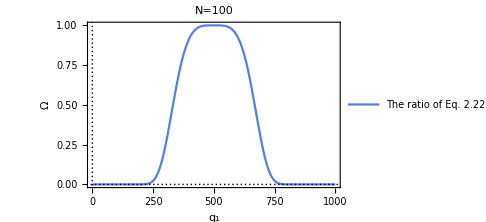

```mathematica
Plot[(Max@apmac[q,100,1000])/(Max@ap2mac[q,100,1000]),{q,0,1000},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"q_1","Ω"},PlotLegends->{"The ratio of Eq. 2.22 / Eq. 2.27"},PlotLabel->"N=100",PlotRange->All,ImageSize->Medium]//Quiet
```

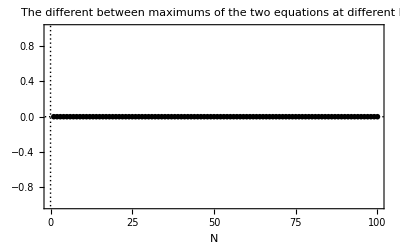

```mathematica
ListLinePlot[Table[Max@Table[apmac[q,s,1000]//N,{q,0,1000}]-Max@Table[ap2mac[q,s,1000],{q,0,1000}]//N,{s,1,100,1}],PlotRange->All,PlotTheme->{"Scientific","BoldColor","Monochrome"},PlotLabel->"The different between maximums of the two equations at different N",FrameLabel->{"N"," "}]//Quiet
```

The approximation is more accurate when N is Large. Moreover, the ratio is 1 around the maximum, which is the place where the two approximations are almost equal. Finally, the maximum of both plots is always the same up to N=100 which I checked. The approximation is valid.

## Problem 4):

### a):

```mathematica
int1[x_,n_]:=x^n Exp[-x];
int2[x_,n_]:=n^n Exp[-n]Exp[-1/2(x-n)^2/n];
```

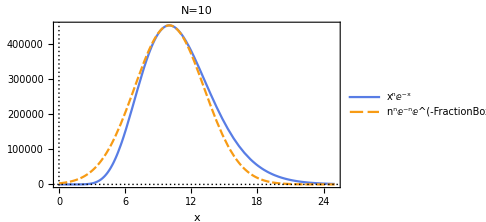

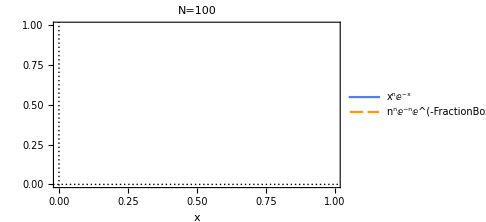

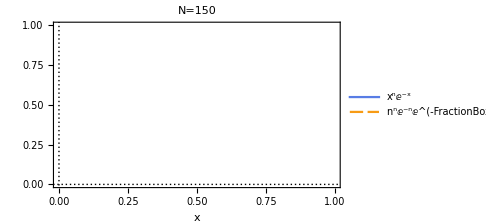

```mathematica
Plot[{int1[x,10.],int2[x,10.]},{x,0,25},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"x"," "},PlotLegends->{"x^nⅇ^-x","n^nⅇ^-nⅇ^(-FractionBox[1, 2] FractionBox[SuperscriptBox[(x - n), 2], n])"},PlotLabel->"N=10",PlotRange->All,ImageSize->Medium,PlotRange->All]//Quiet
Plot[{int1[x,100.],int2[x,100.]},{x,0,250},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"x"," "},PlotLegends->{"x^nⅇ^-x","n^nⅇ^-nⅇ^(-FractionBox[1, 2] FractionBox[SuperscriptBox[(x - n), 2], n])"},PlotLabel->"N=100",PlotRange->All,ImageSize->Medium,PlotRange->All]//Quiet
Plot[{int1[x,150],int2[x,150]},{x,0,375},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"x"," "},PlotLegends->{"x^nⅇ^-x","n^nⅇ^-nⅇ^(-FractionBox[1, 2] FractionBox[SuperscriptBox[(x - n), 2], n])"},PlotLabel->"N=150",PlotRange->All,ImageSize->Medium]//Quiet
```

Only the first two were plottable, I added N=150 instead of the rest because it is the last one I can plot.

### b):

```mathematica
sa={(int1[x,z]-int2[x,z])/(z^z ⅇ^-z)/.z->10,(int1[x,z]-int2[x,z])/(z^z ⅇ^-z)/.z->100,(int1[x,z]-int2[x,z])/(z^z ⅇ^-z)/.z->150};
```

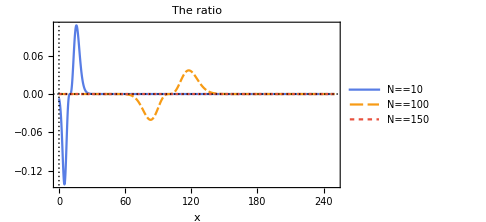

```mathematica
Plot[sa,{x,0,250},PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"x"," "},PlotLegends->{TraditionalForm[N==10],TraditionalForm[N==100],TraditionalForm[N==150]},PlotLabel->"The ratio",PlotRange->All,ImageSize->Medium]//Quiet
```

The difference is negligible when N is big, which means this approximation is valid for big systems.